# NG^23 T_09.Метод обратного распространения ошибки

30-мар-2023
Ковалевская Варвара

## 1. Исходные данные и их стандартизация

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory";
Map[Dimensions,Test=Import["NG23T09Problem.xlsx"]]
Fig0=Uncompress@Test⟦3,1,1⟧;
Dimensions[Train={{#1,#2},Rationalize@#3}&@@@Test⟦1,2;;⟧]
Dimensions[Test={{#1,#2},{##3}}&@@@Test⟦2,2;;⟧]
```

{{4437,3},{1101,5},{1,1}}

{4436,2}

{1100,2}

```mathematica
Train[[;;2]]
```

{{{-0.752585,-0.495197},3},{{0.101878,-0.52802},2}}

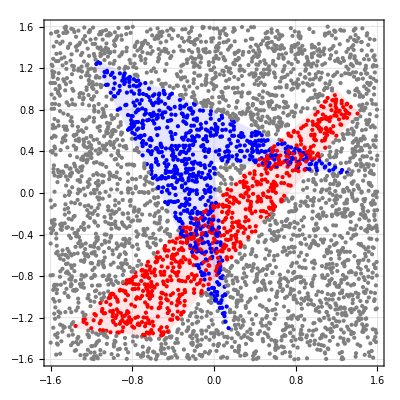

```mathematica
Fig2 =Show[Fig0,Fig1=Graphics[{PointSize@Small,{#2/.{1->Blue,2->Red,3->Gray},Point@#1}&@@@Train}]]
```

## 2. Полносвязная нейронная сеть прямого распространения

LReLU(v):=Piecewise[{{α v, v<0}, {v, 0⩽v}}]

SoftMax(V⃗):=(Exp(V⃗))/(∑_n Exp(V_n))

```mathematica
ClearAll[LReLU,LReLU1,SoftMax];
α=0.01;
LReLU=If[#<0,α #,Min[10.,#]]&
LReLU1=If[#1<0,α,1.]&
SoftMax=Function[#//Exp//#/(Total@#)&//Chop]
```

If[#1<0,α #1,Min[10.,#1]]&

If[#1<0,α,1.]&

Chop[(#1/Total[#1]&)[Exp[#1]]]&

```mathematica
RandomReal[{-1,1},9]
LReLU/@%
Map[LReLU]@%%
Map[LReLU1]@%%%
SoftMax@%%%%
```

{-0.331739,0.18959,-0.943608,0.943862,-0.822139,0.258915,0.578833,0.638015,-0.560477}

{-0.00331739,0.18959,-0.00943608,0.943862,-0.00822139,0.258915,0.578833,0.638015,-0.00560477}

{-0.00331739,0.18959,-0.00943608,0.943862,-0.00822139,0.258915,0.578833,0.638015,-0.00560477}

{0.01,1.,0.01,1.,0.01,1.,1.,1.,0.01}

{0.0660346,0.11122,0.035813,0.23646,0.0404384,0.119204,0.164145,0.174153,0.052533}

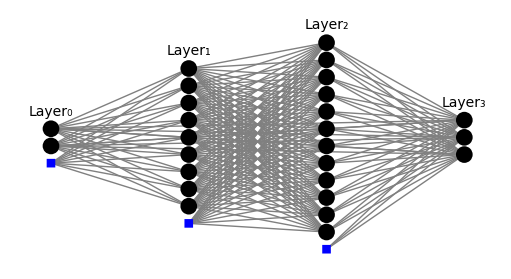
-Graphics-

Рис 2. Трёхслойный персептрон

```mathematica
{2,9,12,3}
Partition[%,2,1]
{#2,#1+1}&@@@%
Map[Dimensions,RandomReal[0.1 {-1,1},#]&/@%]
```

{2,9,12,3}

{{2,9},{9,12},{12,3}}

{{9,3},{12,10},{3,13}}

{{9,3},{12,10},{3,13}}

```mathematica
ClearAll[kmANN];
kmANN["Init",Magnitude_,Signature_]:=Map[Dimensions,kmWeight=Map[RandomReal[ {-Magnitude,Magnitude},#]&,{#2,#1+1}&@@@Partition[Signature,2,1]]];
```

```mathematica
kmANN["Init",0.2,{2,9,12,3}]
```

{{9,3},{12,10},{3,13}}

```mathematica
RandomChoice@Train[[All,1]]
%//Append[#,1.]&//
Dot[kmWeight[[1]],#]&//Map@LReLU//Append[#,1.]&//
Dot[kmWeight[[2]],#]&//Map@LReLU//Append[#,1.]&//
Dot[kmWeight[[3]],#]&//SoftMax
```

{0.763287,-0.054531}

{0.343044,0.310794,0.346162}

```mathematica
ClearAll[kmANN];
kmANN["Init",Magnitude_,Signature_]:=Map[Dimensions,kmWeight=Map[RandomReal[ {-Magnitude,Magnitude},#]&,{#2,#1+1}&@@@Partition[Signature,2,1]]];
kmANN[X_]:=X//Append[#,1.]&//
Dot[kmWeight[[1]],#]&//Map@LReLU//Append[#,1.]&//
Dot[kmWeight[[2]],#]&//Map@LReLU//Append[#,1.]&//
Dot[kmWeight[[3]],#]&//SoftMax
```

```mathematica
RandomChoice@Train
kmANN@First@%
```

{{1.4499,0.410356},3}

{0.345284,0.311194,0.343522}

## 3. Визуализация

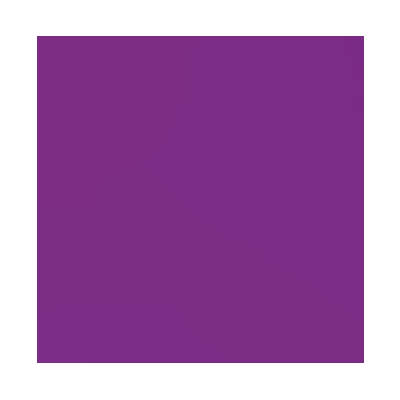

```mathematica
Graphics[{Raster[Table[Blend[{Blue,Red,Gray},kmANN@{x,y}]/.RGBColor[c__]:>{c,.3},{x,-1.6,1.6,0.1},{y,-1.6,1.6,0.1}],1.6 {{-1,-1},{1,1}}]}]
```

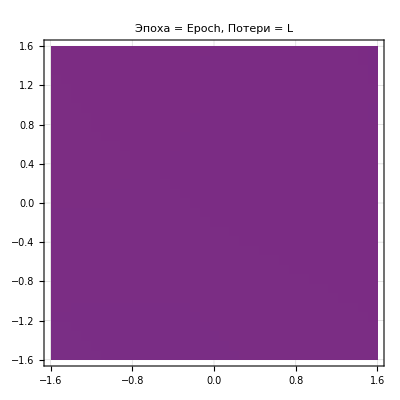

```mathematica
Show[Fig0,Graphics[{Raster[Table[Blend[{Blue,Red,Gray},kmANN@{x,y}]/.RGBColor[c__]:>{c,.3},{x,-1.6,1.6,0.1},{y,-1.6,1.6,0.1}],1.6 {{-1,-1},{1,1}}]}],PlotLabel->StringForm["Эпоха = ``, Потери = ``",Epoch,L]]
```

```mathematica
CreatePalette@Dynamic[Show[Fig0,Graphics[{Raster[Table[Blend[{Blue,Red,Gray},kmANN@{y,x}]/.RGBColor[c__]:>{c,.3},{x,-1.6,1.6,0.1},{y,-1.6,1.6,0.1}],1.6 {{-1,-1},{1,1}}]}],PlotLabel->StringForm["Эпоха = ``, Потери = ``",Epoch,L],ImageSize->200],TrackedSymbols:>{Epoch}]
```

b0a173db-8281-4173-bef4-835e5a953dadUntitled-5

## 4. Прямой ход обучения

```mathematica
ClearAll[kmANN];
kmANN["Init",Magnitude_,Signature_]:=Map[Dimensions,kmWeight=Map[RandomReal[ {-Magnitude,Magnitude},#]&,{#2,#1+1}&@@@Partition[Signature,2,1]]];

kmANN[X_]:=X//Append[#,1.]&//
Dot[kmWeight[[1]],#]&//Map@LReLU//Append[#,1.]&//
Dot[kmWeight[[2]],#]&//Map@LReLU//Append[#,1.]&//
Dot[kmWeight[[3]],#]&//SoftMax;

kmANN[,X_]:=X//Append[#,1.]&//Sow//
Dot[kmWeight[[1]],#]&//Map@LReLU//Append[#,1.]&//Sow//
Dot[kmWeight[[2]],#]&//Map@LReLU//Append[#,1.]&//Sow//
Dot[kmWeight[[3]],#]&//SoftMax//Sow;
```

```mathematica
RandomChoice@Train[[All,1]]
kmANN@%
Reap@kmANN[,%%]
Map[Length,%[[2,1]]]
```

{-0.180198,-1.59605}

{0.33903,0.306477,0.354494}

{{0.33903,0.306477,0.354494},{{{-0.180198,-1.59605,1.},{-0.000766046,0.119376,0.0189739,0.0548341,-0.0032919,0.121606,0.20597,0.240962,-0.00384543,1.},{0.246823,0.0438243,-0.000614475,-0.00284397,-0.00112222,0.0772683,-0.0000196275,-0.00101891,-0.000970876,0.0167411,0.0920892,-0.00122304,1.},{0.33903,0.306477,0.354494}}}}

{3,10,13,3}

## 5. Локальные градиенты

Δ W_(l,n,i)==η Y_(l-1,i)δ_(l,n)

OverVector[δ_out]==OverVector[YT]-OverVector[Y_out]

δ_(l,n)==φ'(V_(l,n))∑_(k∈L_(l+1)) W_(l+1,k,n)δ_(l+1,k)

Используя произвольный тренировочный образец, пошагово вычислите все локальные градиенты. Для этого действуйте следующим образом: 
(а) выполните прямой ход; 
(б) соберите все отклики в переменную Y;

```mathematica
{X,Class}=RandomChoice@Train
Y=Reap[kmANN[,X]][[2,1]]
Map[Length,Y]
```

{{-0.582271,-0.909729},2}

{{-0.582271,-0.909729,1.},{-0.00152093,0.0745324,0.0016842,-0.000313409,-0.00296309,-0.000082618,0.10045,0.221867,-0.0027884,1.},{0.215542,0.0829924,-0.000603012,-0.00246763,-0.00108391,0.0622275,-0.0000404964,-0.000866801,-0.00113048,0.0371189,0.0850769,-0.000834561,1.},{0.341423,0.304966,0.353611}}

{3,10,13,3}

(в) вычислите ошибку нейросети, используя перекрёстную энтропию kmLoss (DisplayFormulaNumbered) в качестве функции потерь;

Loss(W):=-∑_n YT_n Ln(Y_n)

```mathematica
ClearAll[kmLoss];
kmLoss[{X_,Class_}]:= -RealExponent[kmANN[X][[Class]]];
```

```mathematica
kmLoss@{X,Class}
```

0.515748

(г) двигаясь в обратном направлении от выходного слоя ко входному, последовательно слой за слоем, вычислите локальные градиенты всех нейронов (DisplayFormulaNumbered), (DisplayFormulaNumbered) и сохраните их в переменной δ;

OverVector[δ_out]==OverVector[YT]-OverVector[Y_out]

```mathematica
Length@Y
```

4

```mathematica
δ={,,}
δ[[-1]]=UnitVector[3,Class]-Y[[-1]]
```

{Null,Null,Null}

{-0.320905,-0.366757,0.687662}

δ_(l,n)==φ'(V_(l,n))∑_(k∈L_(l+1)) W_(l+1,k,n)δ_(l+1,k)

```mathematica
δ[[-2]]=δ[[-1]].kmWeight[[-1]]
```

{0.0887062,-0.0917529,0.0905226,-0.031506,0.018506,-0.162203,0.0324861,-0.088197,-0.209789,-0.0280933,0.194253,-0.0627935,-0.0567672}

```mathematica
LReLU1/@Y[[2]]
```

{0.01,0.01,1.,1.,1.,0.01,1.,0.01,1.,1.}

```mathematica
δ[[-2]]=Dot[δ[[-1]],kmWeight[[-1]]] Map[LReLU1,Y[[-2]]]
```

{0.0887062,-0.000917529,0.0905226,-0.031506,0.018506,-0.00162203,0.000324861,-0.088197,-0.209789,-0.0280933,0.00194253,-0.0627935,-0.0567672}

```mathematica
δ[[-3]]=Dot[Most@δ[[-2]],kmWeight[[-2]]] Map[LReLU1,Y[[-3]]]
```

{-0.000143723,0.00017935,-0.0142712,-0.00560052,-0.0451607,7.18073×10^-6,-0.0210367,-0.0000174955,-0.0321396,0.0074895}

```mathematica
Dimensions/@δ
```

{{10},{13},{3}}

(д) используя локальные градиенты δ, вычислите поправки ΔW ко всем весам нейросети (DisplayFormulaNumbered).

Δ W_(l,n,i)==η Y_(l-1,i)δ_(l,n)

```mathematica
Length/@Y
```

{3,10,13,3}

```mathematica
ΔW={,,}
Dimensions[ΔW[[1]]=Outer[Times,Most@δ[[1]],Y[[1]]]]
Dimensions[ΔW[[2]]=Outer[Times,Most@δ[[2]],Y[[2]]]]
Dimensions[ΔW[[3]]=Outer[Times,δ[[3]],Y[[3]]]]
Dimensions/@kmWeight
```

{Null,Null,Null}

{9,3}

{12,10}

{3,13}

{{9,3},{12,10},{3,13}}

```mathematica
ClearAll[kmΔWeight];
kmΔWeight[{X_,Class_}]:=Block[{δ,Y=Reap[kmANN[,X]][[2,1]]},
δ={,,UnitVector[3,Class]-Y[[-1]]};
δ[[-2]]=Dot[δ[[-1]],kmWeight[[-1]]] Map[LReLU1,Y[[-2]]];
δ[[-3]]=Dot[Most@δ[[-2]],kmWeight[[-2]]] Map[LReLU1,Y[[-3]]];
{Outer[Times,Most@δ[[1]],Y[[1]]],Outer[Times,Most@δ[[2]],Y[[2]]],Outer[Times,δ[[3]],Y[[3]]]}
]
```

```mathematica
RandomChoice@Train
Map[Dimensions,kmΔWeight@%]
```

{{1.25435,-1.15581},3}

{{9,3},{12,10},{3,13}}

## 6. Обратный ход обучения

```mathematica
ClearAll[kmΔWeight];
kmΔWeight[{X_,Class_}]:=Block[{δ,Y=Reap[kmANN[,X]][[2,1]]},
δ={,,UnitVector[3,Class]-Y[[-1]]};
δ[[-2]]=Dot[δ[[-1]],kmWeight[[-1]]] Map[LReLU1,Y[[-2]]];
δ[[-3]]=Dot[Most@δ[[-2]],kmWeight[[-2]]] Map[LReLU1,Y[[-3]]];
{Outer[Times,Most@δ[[1]],Y[[1]]],Outer[Times,Most@δ[[2]],Y[[2]]],Outer[Times,δ[[3]],Y[[3]]]}
]
```

## 7. Эпоха обучения

```mathematica
Dimensions/@Total[kmΔWeight/@Train[[{1,22,44,657}]]]
```

{{9,3},{12,10},{3,13}}

```mathematica
ClearAll[kmTrain];
iTrain=Range@Length@Train;
T$C=UpTo@Floor[0.8 Length@Train];
kmTrain[miniBatch_ ,η_]:=Block[{iTeach,iCheck,batchCounter},
{iTeach,iCheck}=Partition[RandomSample@iTrain,T$C];
Do[
AddTo[kmWeight,η Total[kmΔWeight/@Train[[batch]]]],
{batch,Partition[iTeach,miniBatch]}];
Total[kmLoss/@Train[[iCheck]]]
];
```

```mathematica
kmTrain[10,0.1]
```

385.782

```mathematica
Dynamic[MatrixPlot/@kmWeight]
```

```mathematica
ClearAll[kmTrain];
lenTrain=Length@Train;
iTrain=Range@lenTrain;
T$C=UpTo@Floor[0.8 lenTrain];
kmTrain[BatchSize_ ,η_]:=Block[{iTeach,iCheck,Step = 0,Steps={1,.8 lenTrain/BatchSize},batchCounter},
{iTeach,iCheck}=Partition[RandomSample@iTrain,T$C];
Do[Step++;
AddTo[kmWeight,η Total[kmΔWeight/@Train[[batch]]]],
{batch,Partition[iTeach,BatchSize]}];
Total[kmLoss/@Train[[iCheck]]]
];
```

```mathematica
kmTrain[10,0.02]
```

186.441

## 8. Обучение классификатора

```mathematica
Epoch=-1; Stop = True;miniBatchSize=10;η=0.02;
kmANN["Init",0.01,{2,9,12,3}]
```

{{9,3},{12,10},{3,13}}

```mathematica
PrintTemporary@Row[{Button["Stop",Stop=False,Method->"Preemptive"],Button["Abort",Abort,Method->"Preemptive"]},Spacer@10];While[Stop,Epoch++;
L = kmTrain[miniBatchSize,η*=.99]
]
```

```mathematica
kmANN@{-0.2,-0.5}
```

{0.306642,0.692124,0.00123418}

```mathematica
kmANN@{0.1,-0.8}
```

{0.483053,0.00328837,0.513659}

## 9. Качество обучения